Quadrupole Trap: using the Anti-Helmholtz coil configuration. The 3D field calculation is obtained from a series expansion of 1/|r-r’|^3 in the (elliptic integral). Nice derivation can be found here: http://publish.illinois.edu/davidchen/files/2012/10/Anti-Helmholtz-magnetic-trap.pdf

Assuming constant current, we can use Biot-Savart’s Law. From there, continue...

```mathematica
B3D[x_,y_,z_] := {x, y, -2*z};
```

```mathematica
VectorPlot3D[B3D[x,y,z],{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

```mathematica
B2D[x_,z_]:={x,-2z};
```

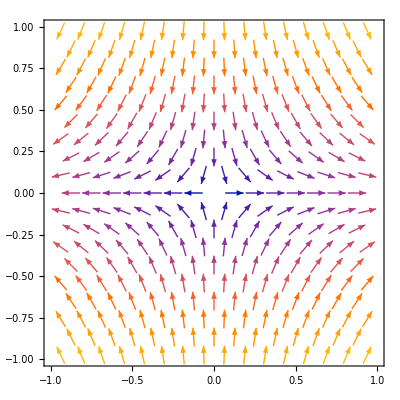

```mathematica
VectorPlot[B2D[x,z],{x,-1,1},{z,-1,1}]
```

```mathematica
NormB3D[x_,y_,z_]:=Norm[B3D[x,y,z]];
```

```mathematica
NormB2D[x_,z_]:=Norm[B2D[x,z]];
```

```mathematica
DensityPlot3D[NormB3D[x,y,z],{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

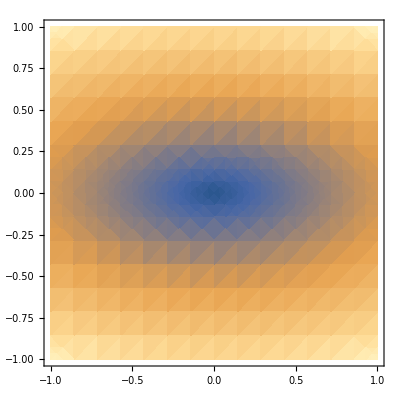

```mathematica
DensityPlot[NormB2D[x,z],{x,-1,1},{z,-1,1}]
```

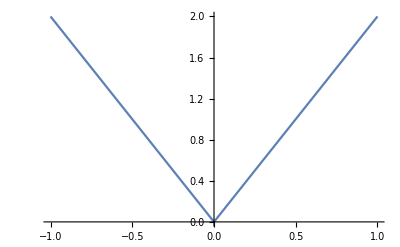

```mathematica
Plot[NormB3D[0,0,z],{z,-1,1}]
```

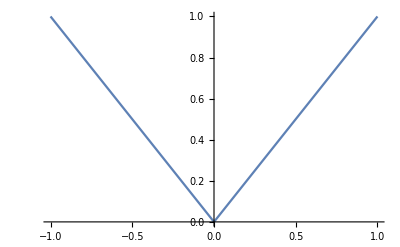

```mathematica
Plot[NormB3D[0,y,0],{y,-1,1}]
```

TOP trap: modifying the quadrupole trap inconvenience by removing the zero point magnetic field. The additional field is an XY-rotating bias field given by

```mathematica
BTime[x_,y_,z_,t_,Omega_] := {B*Cos[Omega*t], B*Sin[Omega*t], 0};
```

```mathematica
BTotal[x_,y_,z_,t_,Omega_]:=A*B3D[x,y,z]+BTime[x,y,z,t,Omega];
```

```mathematica
Norm[BTotal[x,y,z,t,Omega]]
```

√(4 Abs[A z]^2+Abs[A x+B Cos[Omega t]]^2+Abs[A y+B Sin[Omega t]]^2)

After some approximations (r =\sqrt{x^2 + y^2 + z^2} <<  R), the time-averaged magnetic field strength is

```mathematica
B=1;A=2;
```

```mathematica
BTAvg[x_,y_,z_]:=B+(A^2/(4*B))*(x^2+y^2+8*z^2);
```

```mathematica
DensityPlot3D[BTAvg[x,y,z],{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

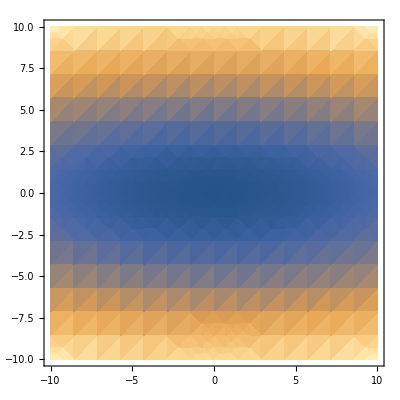

```mathematica
DensityPlot[BTAvg[x,0,z],{x,-10,10},{z,-10,10}]
```

Notice that we now have an effective anisotropic harmonic potential. At the origin, the magnetic field is now B.

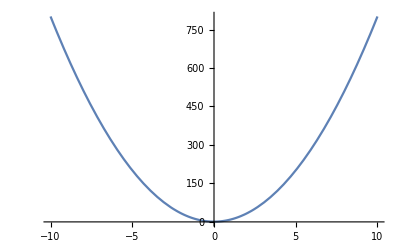

```mathematica
Plot[BTAvg[0,0,z],{z,-10,10}]
```

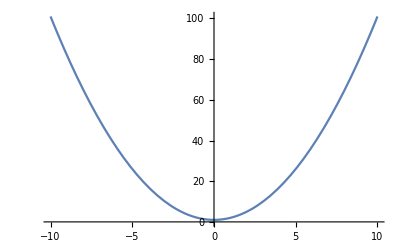

```mathematica
Plot[BTAvg[x,0,0],{x,-10,10}]
```

```mathematica
Plot[BTAvg[0,y,0],{y,-10,10}]
```

-Graphics-

How to use the field strength curvature to calculate \omega_x, \omega_y, \omega_z (trapping frequencies which atoms see)...

C^2*x^2/(4*B) = Bfield = -E/mu=-(m*omega^2*x^2)/(2*mu) ---> \omega_x = \sqrt{-mu*C^2/2mB}

8*C^2*z^2/(4*B) = Bfield = -E/mu=-(m*omega^2*z^2)/(2*mu) ---> \omega_z = \sqrt{-4mu*C^2/mB}

Finally we have the Ioffe-Pritchard trap. See source for the configuration.

```mathematica
a=1;b=1.2;
```

```mathematica
C1=-a^2/(a^2+b^2)^(3/2);C3=a^2*(a^2-4*b^2)/(2*(a^2+b^2)^(7/2));
```

```mathematica
BIP[x_,y_,z_]:={3*C3*z*x,3*C3*z*y,-(C1-(3/2)*C3*(x^2+y^2-2*z^2))};
```

```mathematica
VectorPlot3D[BIP[x,y,z],{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

```mathematica
NormBIP[x_,y_,z_]:=Norm[BIP[x,y,z]]
```

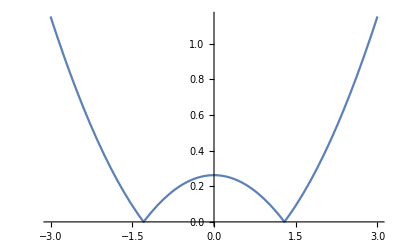

```mathematica
Plot[NormBIP[x,0,0],{x,-3,3}]
```

```mathematica
Plot[NormBIP[0,y,0],{y,-3,3}]
```

-Graphics-

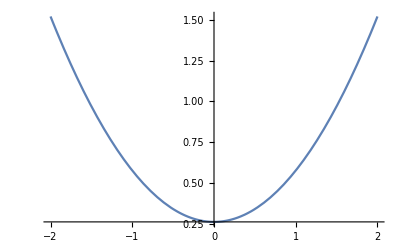

```mathematica
Plot[NormBIP[0,0,z],{z,-2,2}]
```

```mathematica
DensityPlot3D[NormBIP[x,y,z],{x,-3,3},{y,-3,3},{z,-3,3}]
```

-Graphics3D-